```mathematica
ColourForKey[allGraphs4,12]
```

RGBColor[0, Rational[2, 3], 0]

```mathematica
Table[
```

```mathematica
MyColor[n_]:=Part[{Red,Green,Blue,Yellow},Mod[n-1,4]+1]
```

```mathematica
Table[MyColor[k],{k,Range[10]}]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0]}

```mathematica
Subsets
```

Subsets

```mathematica
RecAppend[set_]:=Block[{},
If[Length[set]==1,
Table[{MyColor[k]},{k,1,2}],
Flatten[Table[Table[Prepend[t,MyColor[k]],{t,RecAppend[Rest[set]]}],{k,1,2}],1]
]
]
```

```mathematica
RecAppend2[set_]:=Block[{values=RecAppend[set],record, size,result={},pos},
size=Total[Table[Length[s],{s,set}]];
Table[
record=Range[size];
Table[
Table[
record[[k]]=v[[pos]],
{k,set[[pos]]}
]
,{pos,1,Length[v]}];
record,
{v,values}
]
]
```

```mathematica
ColourTable[set_]:=TableForm[RecAppend2[set],TableSpacing->{0, 0}]
```

```mathematica
TableForm[RecAppend2[{{1,2},{3}}],TableSpacing->{0, 0}]
```

RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[RecAppend[{1,2,3}],TableSpacing->{0, 0}]
```

RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0]
RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0]

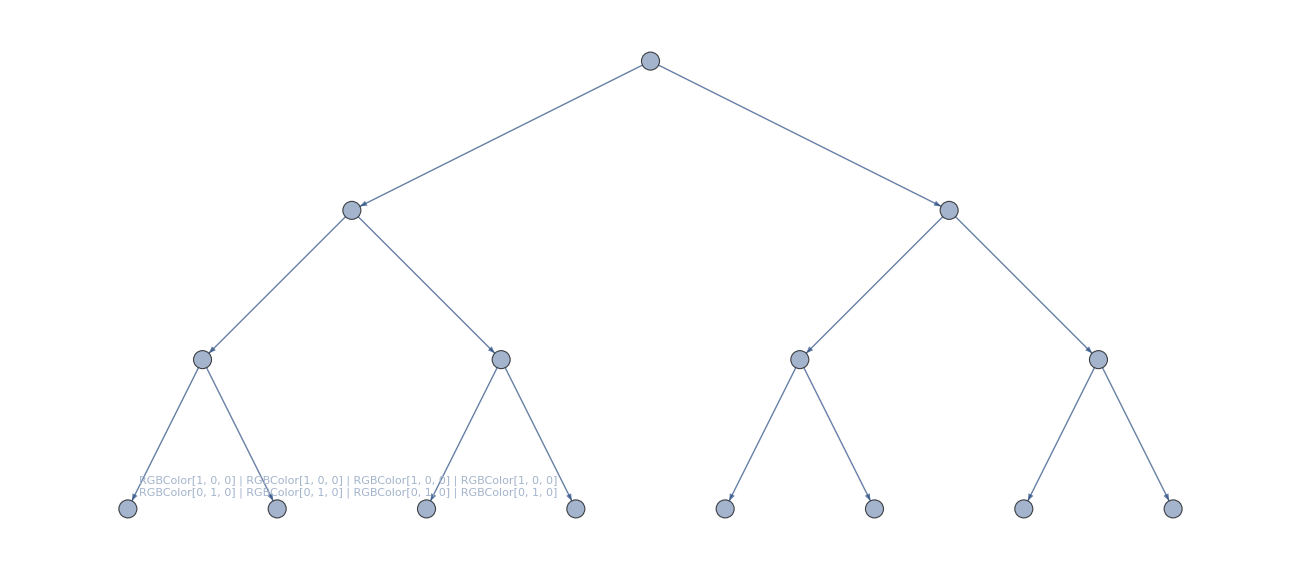

```mathematica
Graph[Table[Framed[
Row[{allGraphs4[e[[1]],"graph"],ColourTable[allGraphs4[e[[1]],"vertexsets"]]}],Background->White]->Framed[
Row[{allGraphs4[e[[2]],"graph"],ColourTable[allGraphs4[e[[2]],"vertexsets"]]}],Background->White],{e,{{271,517},{271,28},{517,637},{517,487},{637,728},{637,546},{487,488},{487,486},{28,110},{28,27},{110,218},{110,2},{27,54},{27,0}}}], VertexLabels->{"Name"}]
```